\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Introduction to Mathematica (MMA) -- 02

Zu-Cheng Chen

Institute of Theoretical Physics, 
Chinese Academy of Sciences

@ Guangzhou University, Jul 2019

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## List

## Create a list

### List

```mathematica
List[1,2,3,4,5]
```

{1,2,3,4,5}

```mathematica
a={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
b={{x1,x2},{y1,y2}}
%//MatrixForm
```

{{x1,x2},{y1,y2}}

(x1 | x2
y1 | y2)

### Table

```mathematica
Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
c=Table[f[i]+f[j],{i,1,3},{j,1,3}]
c//MatrixForm
```

{{2 f[1],f[1]+f[2],f[1]+f[3]},{f[1]+f[2],2 f[2],f[2]+f[3]},{f[1]+f[3],f[2]+f[3],2 f[3]}}

(2 f[1] | f[1]+f[2] | f[1]+f[3]
f[1]+f[2] | 2 f[2] | f[2]+f[3]
f[1]+f[3] | f[2]+f[3] | 2 f[3])

### Range

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[1,10,2]
```

{1,3,5,7,9}

## Access elements

```mathematica
c=Table[f[i]+f[j],{i, 1, 3},{j, 1, 3}]
```

{{2 f[1],f[1]+f[2],f[1]+f[3]},{f[1]+f[2],2 f[2],f[2]+f[3]},{f[1]+f[3],f[2]+f[3],2 f[3]}}

```mathematica
c[[1]]
```

{2 f[1],f[1]+f[2],f[1]+f[3]}

```mathematica
c[[1]][[1]]
```

2 f[1]

```mathematica
c[[1,1]]
```

2 f[1]

## +, -, *, /, ...

```mathematica
a=.
c=.
{a,b,c}+{x,y,z}+t
```

{a+t+x,b+t+y,c+t+z}

```mathematica
{x,y,z}-t
```

{-t+x,-t+y,-t+z}

```mathematica
{a,b,c}*{x,y,z}
```

{a x,b y,c z}

```mathematica
{a,b,c}/{x,y,z}
```

{a/x,b/y,c/z}

```mathematica
{a,b,c}^p
```

{a^p,b^p,c^p}

```mathematica
Log[{a,b,c}]
```

{Log[a],Log[b],Log[c]}

## Attributes

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
Attributes[Minus]
```

{Listable,NumericFunction,Protected}

```mathematica
Attributes[Times]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected}

```mathematica
Attributes[Log]
```

{Listable,NumericFunction,Protected}

## Map == /@

```mathematica
Clear[a,b,c]
list={a,b,c}
f/@list
```

{a,b,c}

{f[a],f[b],f[c]}

```mathematica
Table[f[i],{i,list}]
```

{f[a],f[b],f[c]}

## Flatten

```mathematica
Flatten[{a,b,{c,{d,e},f}}]
```

{a,b,c,d,e,f}

## MemberQ

```mathematica
MemberQ[{a,b,{c,{d,e},f}},a]
```

True

```mathematica
MemberQ[{a,b,{c,{d,e},f}},d]
```

False

```mathematica
MemberQ[{a,b,{c,{d,e},f}},{c,{d,e},f}]
```

True

## Join

```mathematica
Join[{a,b,c},{x,y},{u,v,w}]
```

{a,b,c,x,y,u,v,w}

```mathematica
{a,b,c}~Join~{x,y}~Join~{u,v,w}
```

{a,b,c,x,y,u,v,w}

## Dot

```mathematica
{a,b,c} . {x,y,z}
```

a x+b y+c z

```mathematica
{{a,b},{c,d}} . {x, y}
```

{a x+b y,c x+d y}

```mathematica
{x,y} . {{a,b},{c,d}}
```

{a x+c y,b x+d y}

```mathematica
{{a,b},{c,d}}//MatrixForm
```

(a | b
c | d)

### Exercise

Calculate (8 | 4
3 | 5).(2 | 1
7 | 9)

## Cross

```mathematica
Cross[{1,2,3},{1,1,1}]
```

{-1,2,-1}

## Norm

```mathematica
Norm[{a,b,c}]
```

√(Abs[a]^2+Abs[b]^2+Abs[c]^2)

```mathematica
Normalize[{a,b,c}]
```

{a/(√(Abs[a]^2+Abs[b]^2+Abs[c]^2)),b/(√(Abs[a]^2+Abs[b]^2+Abs[c]^2)),c/(√(Abs[a]^2+Abs[b]^2+Abs[c]^2))}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Everything in MMA is an expression!

## Head

```mathematica
c=a+b
c//Head
```

a+b

Plus

```mathematica
Plus[a,b]
```

a+b

```mathematica
d=f[x+b[y],z*m]
```

f[x+b[y],m z]

```mathematica
d[[0]]
```

f

```mathematica
d[[1]]
```

x+b[y]

## Replace head: @@

```mathematica
c=a+b
f@@c
```

a+b

f[a,b]

```mathematica
d={a,b}
f@@d
```

{a,b}

f[a,b]

## Map

```mathematica
expr=x+y+z+u
Log/@expr
```

u+x+y+z

Log[u]+Log[x]+Log[y]+Log[z]

## FullForm

```mathematica
d//FullForm
```

List[a,b]

## TreeForm

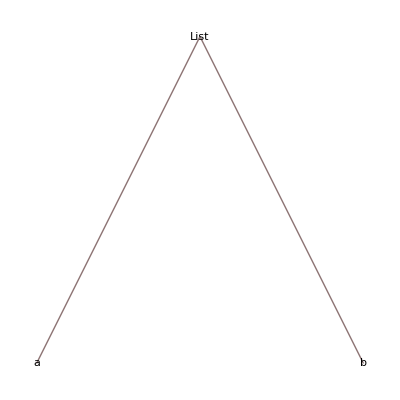

```mathematica
d//TreeForm
```

## Exercise

Consider the following expression:
G[p,q][x,y,z]

How can you access the element q ?

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Rules

## _ : stands for any Wolfram Language expression

```mathematica
rule01=f[x_]->x^2
```

f[x_]→x^2

```mathematica
f[3]
```

f[3]

```mathematica
f[3]/.rule01
```

9

```mathematica
rule02=f[x_]:>x^2
```

f[x_]:>x^2

```mathematica
f[3]/.rule02
```

9

## __ : stands for any sequence of one or more Wolfram Language expressions

```mathematica
rule03=f[x__]:>Plus@x
```

f[x__]:>+x

```mathematica
f[a,b]
```

f[a,b]

```mathematica
f[a,b]/.rule03
```

a+b

```mathematica
f[x__]:=Plus[x]
f[a,b]
```

a+b

## ___ : stands for any sequence of zero or more Wolfram Language expressions

```mathematica
rule04=f[x___]:>Plus@x
```

f[x___]:>+x

```mathematica
f[a,b]
f[a,b]/.rule04
```

f[a,b]

a+b

```mathematica
f[]
f[]/.rule04
```

f[]

0

```mathematica
g[x___]:=Length[{x}]
g[1,3,3,4,5]
g[]
```

5

0

## ReplaceRepeated

```mathematica
Clear@f;
f[5]//.{f[1]->1,f[n_]->n f[n-1]}
```

120

```mathematica
f[5]/.{f[1]->1,f[n_]->n f[n-1]}
```

5 f[4]

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Pure function

```mathematica
f1[x_]:=x^2
```

```mathematica
f2=Function[x,x^2]
f2[y]
```

Function[x,x^2]

y^2

```mathematica
f3=Function[#^2]
f3[y]
```

#1^2&

y^2

```mathematica
f4=#^2&
f4[y]
```

#1^2&

y^2

```mathematica
Sin[5]//N
```

-0.958924

```mathematica
N[Sin[5],10]
```

-0.9589242747

```mathematica
Sin[5]//N[#,10]&
```

-0.9589242747

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Module -- local variable

```mathematica
a=3;
g[x_]:=Module[
{a},
a=x^2+1;
Print[a]
]
```

```mathematica
g[3]
```

10

```mathematica
a
```

3

## Exercise

Rewrite S_n function using Module.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Options

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

## Attributes

```mathematica
Sqrt[x^2]
```

√(x^2)

```mathematica
Attributes[Sqrt]
```

{Listable,NumericFunction,Protected}

```mathematica
Unprotect[Sqrt];
```

```mathematica
Sqrt[x_^2]:=x
```

```mathematica
Sqrt[x^2]
```

x

```mathematica
Protect[Sqrt]
```

```mathematica
f[x_]:=Sin[x^2+2]
```

```mathematica
SetAttributes[f,Protected]
```

```mathematica
f[x_]:=Sin[x^2]
```

SetDelayed::write: Tag f in f[x_] is Protected.

$Failed

```mathematica
Clear@f
```

Clear::wrsym: Symbol f is Protected.

```mathematica
Remove[f]
```

Remove::rmptc: Symbol f is Protected and cannot be removed.

## Default values

```mathematica
h[x_:2,y_:3]:=x/y
```

```mathematica
h[]
```

2/3

```mathematica
h[1]
```

1/3

## Default options

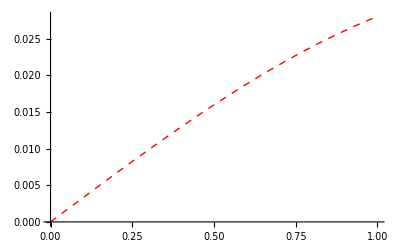

```mathematica
myPlot[xexper_,OptionsPattern[{opp1->3,plotstyle->Directive[Red,Thick,Dashed]}]]:=Plot[xexper/OptionValue[opp1],{x,0,1},PlotStyle->OptionValue[plotstyle]]

myPlot[Sin[x],opp1->30]
```

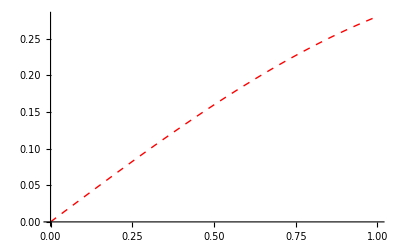

```mathematica
myPlot[Sin[x]]
```

## Usage informations

```mathematica
test[x_]:=x^2
test::usage="This is a test function";
```

```mathematica
test[3]
```

9

```mathematica
?test
```

```mathematica
??test
```

## Compile

```mathematica
f=Function[{x,n},Sin[x]+x^n];
```

```mathematica
cf= Compile[{{x, _Real},{n,_Integer}}, Sin[x] + x^n,Parallelization->True];
```

```mathematica
Timing[Do[f[1.0,2],{100000}]]
Timing[Do[cf[1.0,2],{100000}]]
```

{0.176735,Null}

{0.03982,Null}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Visualization

## Plot

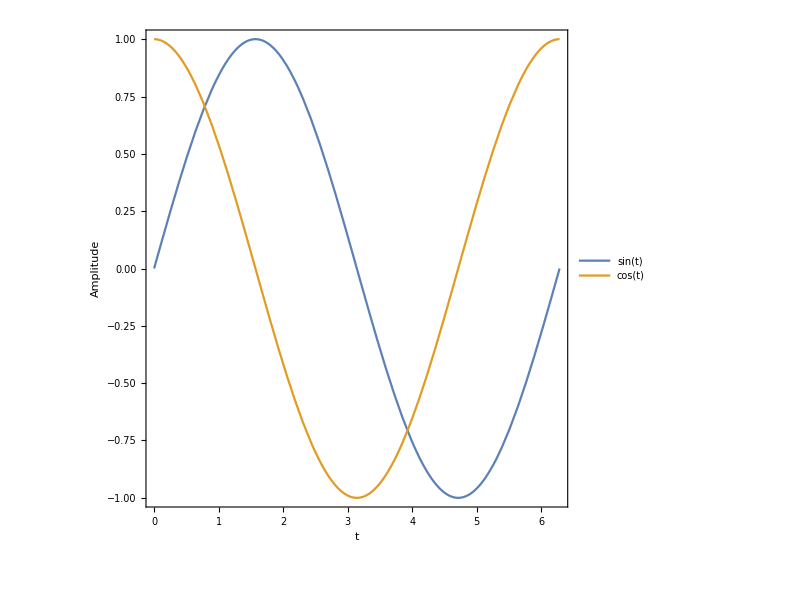

```mathematica
Plot[{Sin[t],Cos[t]},{t,0,2*π},Frame->True,PlotLegends->"Expressions",FrameLabel->{"t","Amplitude"},BaseStyle->Large,ImageSize->600,AspectRatio->1]
```

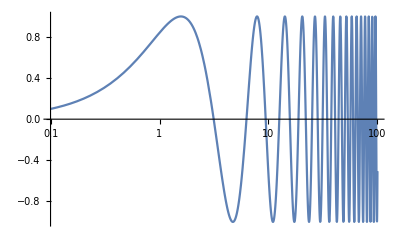

```mathematica
LogLinearPlot[Sin[x],{x,10^-1,10^2},PlotRange->All]
```

```mathematica
Plot3D[Sin[x]*Cos[y],{x,0,2*π},{y,0,2*π},AxesLabel->Automatic]
```

-Graphics3D-

## ListPlot

```mathematica
data=Table[{x,Sin[x]},{x,0,2*π,0.1}];
```

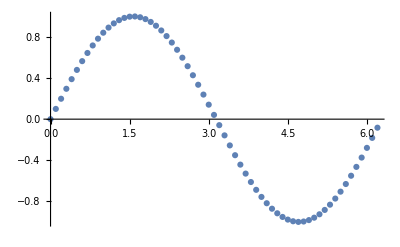

```mathematica
ListPlot[data]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Parallel

```mathematica
Clear@f;
f[x_?NumericQ]:=NIntegrate[x*Sin[y+x]*Cos[y],{y,1,10}]
```

```mathematica
f[1]//AbsoluteTiming
```

{0.133843,3.67605}

```mathematica
LaunchKernels[8]
```

PacletInstall::dwnld: An error occurred downloading paclet CloudObject-12.0.907 from site http://pacletserver.wolfram.com: Network error. Could not resolve host: pacletserver.wolfram.com

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
xs=Range[2*10^3];
```

```mathematica
f/@xs;//AbsoluteTiming
```

{13.6463,Null}

```mathematica
Map[f,xs];//AbsoluteTiming
```

{13.5662,Null}

```mathematica
Distribute@f;
```

```mathematica
(ParallelMap[f,xs]);//AbsoluteTiming
```

{3.11793,Null}

```mathematica
(data=ParallelTable[{x,f[x]},{x,xs}];)//AbsoluteTiming
```

{3.11931,Null}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Import/Export

Create a "backup" directory

```mathematica
SetDirectory[NotebookDirectory[]];

If[Not[DirectoryQ["backup"]],CreateDirectory["backup"]];
```

```mathematica
Export["backup/data.m",data]
```

backup/data.m

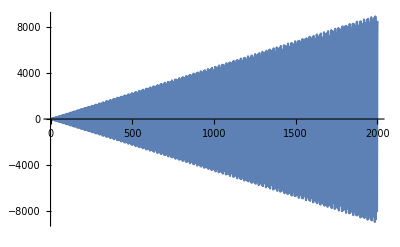

```mathematica
data=Import["backup/data.m"];
ListPlot[data,Joined->True]
```

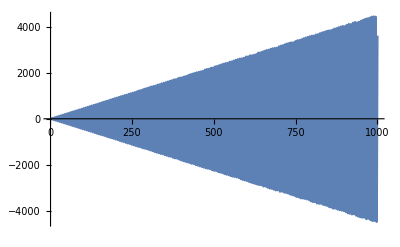
{20.7643,-Graphics-}

```mathematica
Plot[f[x],{x,1,1000}]//AbsoluteTiming
```